Verification of the BAE off formulae for nondegenerate internal squeezing
And 4x4 combined readout

```mathematica
(*BAE adds in complications that are too much for this project, let's drop it
--> sanity check denominator which appears to requires ρBAE unlike dIS, re-do derivation with no BAE to make sure*)
$Assumptions={Ω≥0,γa≥0,γbtot≥γR>0,γc≥0,1>Rpd≥0,χ≥0,ωs>0,β∈Reals,ρRP≥0,αOG∈Reals,ϕ∈Reals};
(*where β=(αGW Larm)/(2^(1/2)ℏ), ρRP=αGW^2/(2^(1/2)ℏ μ);*)

Id=IdentityMatrix[2];
(*simplifying upstream to better the end result*)
Ma=(γa-ⅈ Ω)Id+(ⅈ ρRP)/(2^(1/2)Ω^2)({{1, 1}, {-1, -1}});
invMa=Inverse[Ma]//Simplify;
Mc=(γc-ⅈ Ω)Id; (*manually removed BAE: -(ⅈ ρBAE)/(2^(1/2)Ω^2)({{1, 1}, {-1, -1}})*)
invMc=Inverse[Mc]//Simplify;
Mb=(γbtot-ⅈ Ω)Id+ωs^2 invMa-χ^2({{0, ⅈ Exp[ⅈ ϕ]}, {-ⅈ Exp[-ⅈ ϕ], 0}}).invMc.({{0, ⅈ Exp[ⅈ ϕ]}, {-ⅈ Exp[-ⅈ ϕ], 0}});(*ϕ free in Hamiltonian, recover when ϕ=π/2*)
TimeConstraint0={0.1,1};
invMb=Simplify[Inverse[Mb],TimeConstraint->TimeConstraint0];

Γ=1/2^(1/2)({{1, 1}, {-ⅈ, ⅈ}});
Rin=Simplify[((1-Rpd)^(1/2)Γ.(Id-2 γR invMb).Inverse[Γ]),TimeConstraint->TimeConstraint0];
Rb=Simplify[(-(1-Rpd)^(1/2)(2 γR)^(1/2)(2 (γbtot-γR))^(1/2)Γ. invMb.Inverse[Γ]),TimeConstraint->TimeConstraint0];
Ra=Simplify[(-(1-Rpd)^(1/2)(2 γR)^(1/2)ωs (2 γa)^(1/2)Γ. invMb.invMa.Inverse[Γ]),TimeConstraint->TimeConstraint0];
Rc=Simplify[(-(1-Rpd)^(1/2)(2 γR)^(1/2)(-χ)(2 γc)^(1/2)Γ.invMb.({{0, ⅈ Exp[ⅈ ϕ]}, {-ⅈ Exp[-ⅈ ϕ], 0}}).invMc.Inverse[Γ]),TimeConstraint->TimeConstraint0];(*ϕ free in Hamiltonian, recover when ϕ=π/2*)
T=Simplify[(-(1-Rpd)^(1/2)(2 γR)^(1/2)ωs (-ⅈ β)Γ. invMb.invMa.({{1, 0}, {0, -1}})),TimeConstraint->TimeConstraint0];

(*theorem: conjugation commutes with any holomorphic function that is real-valued on the reals, which is all the functions we care about (check this!), use FlipI only if all variables are real*)
(*look at //FullForm, ⅈ is not present in all forms, sometimes is just Complex[0,1]*)
(*:> is RuleDelayed: "represents a rule that transforms lhs to rhs, evaluating rhs only after the rule is used. "*)
FlipI={ⅈ->-ⅈ,Complex[RePart_,ImPart_]->Complex[RePart,-ImPart]};
(*FlipI should catch all cases (check this with FullForm?, how? --> will not work through Hold, so don't use that)*)
ConjugateFlipI=Conjugate[f_]:>(f/.FlipI);
Sx=Simplify[(
Rpd Id
+Rin.ConjugateTranspose[Rin]
+Ra.ConjugateTranspose[Ra]
+Rb.ConjugateTranspose[Rb]
+Rc.ConjugateTranspose[Rc])/.ConjugateFlipI,TimeConstraint->{1,5}];
(*signal transfer function is Subscript[X, PD,2] wrt h not (X⃗)_PD wrt h⃗ --> factor of two from Subscript[(T.({{1}, {1}})), 22] versus Subscript[T, 22]
NB: another subtlety in that Subscript[T, 21]=Subscript[T, 22], but I don't know if this can be known a priori*)
sigTransfer = Simplify[(T.({{1}, {1}}))[[2]][[1]],TimeConstraint->{1,5}];(*[[1]] to remove atomic brackets {...}*)
sigTransferAbs= Simplify[ComplexExpand[Abs[sigTransfer]],TimeConstraint->{1,5}];
Sh=Simplify[Sx[[2,2]]/sigTransferAbs^2,TimeConstraint->{1,5}];
```

Simplify::gtime: Returning the simplest form found in the allowed time of 1. seconds. Increasing the value of the TimeConstraint option may improve the result of simplification.

```mathematica
Block[{noiseΔSx=Together[Sx[[2,2]]-1]},
SimplifyConstrained=FullSimplify[#,TimeConstraint->{0.1,1}]&;
numerΔSx=Collect[Numerator[noiseΔSx],{ϕ,ρRP},SimplifyConstrained];
denomΔSx=Collect[Denominator[noiseΔSx],{ϕ,ρRP},SimplifyConstrained];]
Print["Sx = 1 + ",numerΔSx,"\n/\n",denomΔSx//Expand//FullSimplify,"\n"]

Block[{sigTsqr=Together[sigTransferAbs^2]},
SimplifyConstrained=FullSimplify[#,TimeConstraint->{0.1,1}]&;
numerTsqr=Collect[Numerator[sigTsqr],{ϕ,ρRP},SimplifyConstrained];
denomTsqr=Collect[Denominator[sigTsqr],{ϕ,ρRP},SimplifyConstrained];]
Print["|T|^2 = ",numerTsqr,"\n/\n",denomTsqr]
```

FullSimplify::time: Time spent on a transformation exceeded 0.1 seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

Sx = 1 + -8 (-1+Rpd) γR ρRP^2 (γc^2+Ω^2) ωs^2 (γa ((-γbtot γc+χ^2)^2+(γbtot^2+γc^2+2 χ^2) Ω^2+Ω^4)+(γc χ^2+γbtot (γc^2+Ω^2)) ωs^2)-8 (-1+Rpd) γc γR χ^2 Ω^4 (γa^2+Ω^2) ((γa^2+Ω^2) ((-γbtot γc+χ^2)^2+(γbtot^2+γc^2+2 χ^2) Ω^2+Ω^4)-2 (γa γc χ^2-γa γbtot (γc^2+Ω^2)+Ω^2 (γc^2+χ^2+Ω^2)) ωs^2+(γc^2+Ω^2) ωs^4)
/
Ω^4 ((γa^2+Ω^2) ((-γbtot γc+χ^2)^2+(γbtot^2+γc^2+2 χ^2) Ω^2+Ω^4)-2 (γa γc χ^2-γa γbtot (γc^2+Ω^2)+Ω^2 (γc^2+χ^2+Ω^2)) ωs^2+(γc^2+Ω^2) ωs^4)^2

|T|^2 = -4 (-1+Rpd) β^2 γR (γc^2+Ω^2) ωs^2
/
(γa^2+Ω^2) ((-γbtot γc+χ^2)^2+(γbtot^2+γc^2+2 χ^2) Ω^2+Ω^4)-2 (γa γc χ^2-γa γbtot (γc^2+Ω^2)+Ω^2 (γc^2+χ^2+Ω^2)) ωs^2+(γc^2+Ω^2) ωs^4

```mathematica
Block[{ρRP=0},
Print[1+numerΔSx/denomΔSx//FullSimplify];
Print[numerTsqr/denomTsqr];
Print[Sh//FullSimplify];]
```

1-(8 (-1+Rpd) γc γR χ^2 (γa^2+Ω^2))/((γa^2+Ω^2) ((-γbtot γc+χ^2)^2+(γbtot^2+γc^2+2 χ^2) Ω^2+Ω^4)-2 (γa γc χ^2-γa γbtot (γc^2+Ω^2)+Ω^2 (γc^2+χ^2+Ω^2)) ωs^2+(γc^2+Ω^2) ωs^4)

-(4 (-1+Rpd) β^2 γR (γc^2+Ω^2) ωs^2)/((γa^2+Ω^2) ((-γbtot γc+χ^2)^2+(γbtot^2+γc^2+2 χ^2) Ω^2+Ω^4)-2 (γa γc χ^2-γa γbtot (γc^2+Ω^2)+Ω^2 (γc^2+χ^2+Ω^2)) ωs^2+(γc^2+Ω^2) ωs^4)

-((γa^2+Ω^2) (-2 γbtot γc χ^2-8 (-1+Rpd) γc γR χ^2+γc^2 Ω^2+γbtot^2 (γc^2+Ω^2)+(χ^2+Ω^2)^2)-2 (γa γc χ^2-γa γbtot (γc^2+Ω^2)+Ω^2 (γc^2+χ^2+Ω^2)) ωs^2+(γc^2+Ω^2) ωs^4)/(4 (-1+Rpd) β^2 γR (γc^2+Ω^2) ωs^2)

```mathematica
Sx/.{ωs->0,χ->γbtot x}//FullSimplify//MatrixForm
(*cf. nOPO:
({{1-(8 (-1+Rpd) x^2 κa^2 κaf κc)/(κa^2 (-x^2 κa+κc)^2+((1+2 x^2) κa^2+κc^2) Ω^2+Ω^4), 0}, {0, 1-(8 (-1+Rpd) x^2 κa^2 κaf κc)/(κa^2 (-x^2 κa+κc)^2+((1+2 x^2) κa^2+κc^2) Ω^2+Ω^4)}})*)
```

(1-(8 (-1+Rpd) x^2 γbtot^2 γc γR)/(γbtot^2 (-x^2 γbtot+γc)^2+((1+2 x^2) γbtot^2+γc^2) Ω^2+Ω^4) | 0
0 | 1-(8 (-1+Rpd) x^2 γbtot^2 γc γR)/(γbtot^2 (-x^2 γbtot+γc)^2+((1+2 x^2) γbtot^2+γc^2) Ω^2+Ω^4))

```mathematica
(*4x4 solution
--> verifying RP and pump phase dependence (or lack thereof) of transfer functions
--> allows for combined signal-idler readout*)
$Assumptions={Ω≥0,γa≥0,γbtot≥γbR>0,γctot≥γcR≥0,1>Rpd≥0,χ≥0,ωs≥0,β∈Reals,ρRP≥0,αOG∈Reals,ϕ∈Reals,ψ0∈Reals,ψ1∈Reals,ψ2∈Reals};
(*where β=(αGW Larm)/(2^(1/2)ℏ), ρRP=αGW^2/(2^(1/2)ℏ μ);*)

Id4=IdentityMatrix[4];
(*simplifying upstream to better the end result*)
Ma=(γa-ⅈ Ω)Id4+(ⅈ ρRP)/(2^(1/2)Ω^2)({{1, 1, 0, 0}, {-1, -1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
invMa=Inverse[Ma]//Simplify;
(*diagonal matrices are not in the centre of the matrix algebra, only multiples of the identity are --> silly mistake!*)
Mb=({{γbtot, 0, 0, 0}, {0, γbtot, 0, 0}, {0, 0, γctot, 0}, {0, 0, 0, γctot}})-ⅈ Ω Id4+χ({{0, 0, 0, ⅈ Exp[ⅈ ϕ]}, {0, 0, -ⅈ Exp[-ⅈ ϕ], 0}, {0, ⅈ Exp[ⅈ ϕ], 0, 0}, {-ⅈ Exp[-ⅈ ϕ], 0, 0, 0}})+ωs^2({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}).invMa.({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});(*ϕ free in Hamiltonian, recover when ϕ=π/2*)
TimeConstraint0={0.1,1};
invMb=Simplify[Inverse[Mb],TimeConstraint->TimeConstraint0];

Γ4=1/2^(1/2)({{1, 1, 0, 0}, {-ⅈ, ⅈ, 0, 0}, {0, 0, 1, 1}, {0, 0, -ⅈ, ⅈ}});
Rin=Simplify[(1-Rpd)^(1/2)Γ4.(Id4-2 ({{γbR^(1/2), 0, 0, 0}, {0, γbR^(1/2), 0, 0}, {0, 0, γcR^(1/2), 0}, {0, 0, 0, γcR^(1/2)}}).invMb.({{γbR^(1/2), 0, 0, 0}, {0, γbR^(1/2), 0, 0}, {0, 0, γcR^(1/2), 0}, {0, 0, 0, γcR^(1/2)}})).Inverse[Γ4],TimeConstraint->TimeConstraint0];
Ra=Simplify[-(1-Rpd)^(1/2) 2ωs γa^(1/2) Γ4.({{γbR^(1/2), 0, 0, 0}, {0, γbR^(1/2), 0, 0}, {0, 0, γcR^(1/2), 0}, {0, 0, 0, γcR^(1/2)}}).invMb.({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}).invMa.({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}).Inverse[Γ4],TimeConstraint->TimeConstraint0];
Rb=Simplify[-(1-Rpd)^(1/2)2Γ4.({{γbR^(1/2), 0, 0, 0}, {0, γbR^(1/2), 0, 0}, {0, 0, γcR^(1/2), 0}, {0, 0, 0, γcR^(1/2)}}).invMb.({{(γbtot-γbR)^(1/2), 0, 0, 0}, {0, (γbtot-γbR)^(1/2), 0, 0}, {0, 0, (γctot-γcR)^(1/2), 0}, {0, 0, 0, (γctot-γcR)^(1/2)}}).Inverse[Γ4],TimeConstraint->TimeConstraint0];(*ϕ free in Hamiltonian, recover when ϕ=π/2*)
T=Simplify[-(1-Rpd)^(1/2)2^(1/2)ωs (-ⅈ β)Γ4.({{γbR^(1/2), 0, 0, 0}, {0, γbR^(1/2), 0, 0}, {0, 0, γcR^(1/2), 0}, {0, 0, 0, γcR^(1/2)}}).invMb.({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}).invMa.({{1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}),TimeConstraint->TimeConstraint0]; (*last matrix is more like ({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}).({{1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}})*)
(*mixed readout, linear combination of all Xpd quadratures is possible,
Xcom = C24.Xpd, Xcom=({{Xcom1}, {Xcom2}}) is 2x1, Xpd=({{Xb1}, {Xb2}, {Xc1}, {Xc2}}) is 4x1, therefore C24 is 2x4,
ψ0=π/2 makes signal just Xb2 since Xb1 doesn't have GW signal (still might not be optimal) ψ1=ϕ maximises GW signal in idler but might not be overall optimal, ψ2=0 is signal readout, ψ2=π/2 is idler readout, anything in-between will have the transfer functions pick up on covariances introduced*)
C24=({{Cos[ψ2] Cos[ψ0], Cos[ψ2]Sin[ψ0], Sin[ψ2] Cos[ψ1], Sin[ψ2]Sin[ψ1]}, {-Sin[ψ2]Cos[ψ0], -Sin[ψ2]Sin[ψ0], Cos[ψ2] Cos[ψ1], Cos[ψ2] Sin[ψ1]}});

(*theorem: conjugation commutes with any holomorphic function that is real-valued on the reals, which is all the functions we care about (check this!), use FlipI only if all variables are real*)
(*look at //FullForm, ⅈ is not present in all forms, sometimes is just Complex[0,1]*)
(*:> is RuleDelayed: "represents a rule that transforms lhs to rhs, evaluating rhs only after the rule is used. "*)
FlipI={ⅈ->-ⅈ,Complex[RePart_,ImPart_]->Complex[RePart,-ImPart]};
(*FlipI should catch all cases (check this with FullForm?, how? --> will not work through Hold, so don't use that)*)
ConjugateFlipI=Conjugate[f_]:>(f/.FlipI);

(* signal readout is just SxCom with ψ0=π/2, ψ2=0;
Sx=Simplify[(
Rpd Id4
+Rin.ConjugateTranspose[Rin]
+Ra.ConjugateTranspose[Ra]
+Rb.ConjugateTranspose[Rb])/.ConjugateFlipI,TimeConstraint->{1,5}];
sigTransferAbs= Simplify[ComplexExpand[Abs[ Simplify[(T.({{1}, {1}, {0}, {0}}))[[2]][[1]],TimeConstraint->{1,5}]]],TimeConstraint->{1,5}];
Sh=Simplify[Sx[[2,2]]/sigTransferAbs^2,TimeConstraint->{1,5}];*)

(*4x4 reduced down to 2x2 by combining readout quadratures*)
SxCom=Simplify[(
Rpd C24.ConjugateTranspose[C24]
+C24.Rin.ConjugateTranspose[Rin].ConjugateTranspose[C24]
+C24.Ra.ConjugateTranspose[Ra].ConjugateTranspose[C24]
+C24.Rb.ConjugateTranspose[Rb].ConjugateTranspose[C24])/.ConjugateFlipI,TimeConstraint->{1,5}];
(*signal transfer function is Subscript[X, PD,2] wrt h not (X⃗)_PD wrt h⃗ --> factor of two from Subscript[(T.({{1}, {1}})), 22] versus Subscript[T, 22]
NB: another subtlety in that Subscript[T, 21]=Subscript[T, 22], but I don't know if this can be known a priori*)
sigTransferCom = Simplify[(C24.T.({{1}, {1}, {0}, {0}}))[[1]][[1]],TimeConstraint->{1,5}];(*[[1]] to remove atomic brackets {...}*)
sigTransferAbsCom= Simplify[ComplexExpand[Abs[sigTransferCom]],TimeConstraint->{1,5}];
ShCom=Simplify[SxCom[[1,1]]/sigTransferAbsCom^2,TimeConstraint->{1,5}];
```

Simplify::gtime: Returning the simplest form found in the allowed time of 1. seconds. Increasing the value of the TimeConstraint option may improve the result of simplification.

Simplify::time: Time spent on a transformation exceeded 0.1 seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

Simplify::gtime: Returning the simplest form found in the allowed time of 1. seconds. Increasing the value of the TimeConstraint option may improve the result of simplification.

Simplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

Simplify::gtime: Returning the simplest form found in the allowed time of 5. seconds. Increasing the value of the TimeConstraint option may improve the result of simplification.

Simplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

Simplify::gtime: Returning the simplest form found in the allowed time of 5. seconds. Increasing the value of the TimeConstraint option may improve the result of simplification.

Simplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

Simplify::gtime: Returning the simplest form found in the allowed time of 5. seconds. Increasing the value of the TimeConstraint option may improve the result of simplification.

```mathematica
(*fix angles*)
signalReadout={ψ0->π/2,ψ2->0};
idlerReadout={ϕ->π/2,ψ1->(*=ϕ=*)π/2,ψ2->π/2};

(*signal function retains total freedom in four angles: ϕ,ψ0,ψ1,ψ2*)
Block[{sigTsqrCom=Together[sigTransferAbsCom^2]},
SimplifyConstrained=FullSimplify[#,TimeConstraint->{0.1,1}]&;
numerTsqrCom=Collect[Numerator[sigTsqrCom],{ϕ,ρRP},SimplifyConstrained];
denomTsqrcom=Collect[Denominator[sigTsqrCom],{ϕ,ρRP},SimplifyConstrained];]
sigTsqrComSimpl=numerTsqrCom/denomTsqrcom;
Clear[numerTsqrCom,denomTsqrcom]

(*simplifying idler and signal readout noise functions separately, too complex otherwise*)
Block[{noiseΔSx=Together[-1+SxCom[[1,1]]/.signalReadout]},
SimplifyConstrained=FullSimplify[#,TimeConstraint->{0.1,1}]&;
numerΔSx4x4=Collect[Numerator[noiseΔSx],{ϕ,ρRP},SimplifyConstrained];
denomΔSx4x4=Collect[Denominator[noiseΔSx]//Expand//Simplify,{ϕ,ρRP},SimplifyConstrained];]
SxSignal=1+numerΔSx4x4/denomΔSx4x4;
Clear[numerΔSx4x4,denomΔSx4x4]
(*I verified that ρRP does not appear in the denominator for nIS*)

(*fast plotter assumes /.{ψ0->π/2(*only Xb2*),ψ1->ϕ(*best idler for GW signal but not noise*),ψ2->π/2(*idler readout*)}/.ϕ->π/2*)
Block[{noiseΔSxComNoFree=Together[-1+SxCom[[1,1]]/.idlerReadout]},
SimplifyConstrained=FullSimplify[#,TimeConstraint->{0.1,1}]&;
numerΔSxComNoFree=Collect[Numerator[noiseΔSxComNoFree],{ϕ,ρRP},SimplifyConstrained];
denomΔSxComNoFree=Collect[Denominator[noiseΔSxComNoFree]//Expand//Simplify,{ϕ,ρRP},SimplifyConstrained];]
SxIdler=1+numerΔSxComNoFree/denomΔSxComNoFree;
Clear[numerΔSxComNoFree,denomΔSxComNoFree]
```

FullSimplify::gtime: Returning the simplest form found in the allowed time of 1. seconds. Increasing the value of the TimeConstraint option may improve the result of simplification.

```mathematica
(*compare signal and idler readouts*)
Print["combined readout, sig. transfer fn.: \n","|T|^2 = ",sigTsqrComSimpl]
Print["signal readout (for ψ0=π/2, ψ2=0): \n","Sx = ",SxSignal,"\n|T|^2 = ",sigTsqrComSimpl/.signalReadout]
Print["idler readout (for ψ1=ϕ=π/2, ψ2=π/2): \n","Sx = ",SxIdler,"\n|T|^2 = ",sigTsqrComSimpl/.idlerReadout]
```

combined readout, sig. transfer fn.: 
|T|^2 = -(4 (-1+Rpd) β^2 ωs^2 (γbR (γctot^2+Ω^2) Cos[ψ2]^2 Sin[ψ0]^2+χ Cos[ϕ-ψ1] (γcR χ Cos[ϕ-ψ1] Sin[ψ2]^2-√(γbR γcR) γctot Sin[ψ0] Sin[2 ψ2])))/((γa^2+Ω^2) ((-γbtot γctot+χ^2)^2+(γbtot^2+γctot^2+2 χ^2) Ω^2+Ω^4)-2 (γa γctot χ^2-γa γbtot (γctot^2+Ω^2)+Ω^2 (γctot^2+χ^2+Ω^2)) ωs^2+(γctot^2+Ω^2) ωs^4)

signal readout (for ψ0=π/2, ψ2=0): 
Sx = 1+(-8 (-1+Rpd) γbR ρRP^2 (γctot^2+Ω^2) ωs^2 (γa ((-γbtot γctot+χ^2)^2+(γbtot^2+γctot^2+2 χ^2) Ω^2+Ω^4)+(γctot χ^2+γbtot (γctot^2+Ω^2)) ωs^2)-8 (-1+Rpd) γbR γctot χ^2 Ω^4 (γa^2+Ω^2) ((γa^2+Ω^2) ((-γbtot γctot+χ^2)^2+(γbtot^2+γctot^2+2 χ^2) Ω^2+Ω^4)-2 (γa γctot χ^2-γa γbtot (γctot^2+Ω^2)+Ω^2 (γctot^2+χ^2+Ω^2)) ωs^2+(γctot^2+Ω^2) ωs^4))/(Ω^4 ((γa^2+Ω^2) ((-γbtot γctot+χ^2)^2+(γbtot^2+γctot^2+2 χ^2) Ω^2+Ω^4)-2 (γa γctot χ^2-γa γbtot (γctot^2+Ω^2)+Ω^2 (γctot^2+χ^2+Ω^2)) ωs^2+(γctot^2+Ω^2) ωs^4)^2)
|T|^2 = -(4 (-1+Rpd) β^2 γbR (γctot^2+Ω^2) ωs^2)/((γa^2+Ω^2) ((-γbtot γctot+χ^2)^2+(γbtot^2+γctot^2+2 χ^2) Ω^2+Ω^4)-2 (γa γctot χ^2-γa γbtot (γctot^2+Ω^2)+Ω^2 (γctot^2+χ^2+Ω^2)) ωs^2+(γctot^2+Ω^2) ωs^4)

idler readout (for ψ1=ϕ=π/2, ψ2=π/2): 
Sx = 1+(-8 (-1+Rpd) γcR ρRP^2 χ^2 ωs^2 (γa ((-γbtot γctot+χ^2)^2+(γbtot^2+γctot^2+2 χ^2) Ω^2+Ω^4)+(γctot χ^2+γbtot (γctot^2+Ω^2)) ωs^2)-8 (-1+Rpd) γcR χ^2 Ω^4 (γbtot (γa^2+Ω^2)+γa ωs^2) ((γa^2+Ω^2) ((-γbtot γctot+χ^2)^2+(γbtot^2+γctot^2+2 χ^2) Ω^2+Ω^4)-2 (γa γctot χ^2-γa γbtot (γctot^2+Ω^2)+Ω^2 (γctot^2+χ^2+Ω^2)) ωs^2+(γctot^2+Ω^2) ωs^4))/(Ω^4 ((γa^2+Ω^2) ((-γbtot γctot+χ^2)^2+(γbtot^2+γctot^2+2 χ^2) Ω^2+Ω^4)-2 (γa γctot χ^2-γa γbtot (γctot^2+Ω^2)+Ω^2 (γctot^2+χ^2+Ω^2)) ωs^2+(γctot^2+Ω^2) ωs^4)^2)
|T|^2 = -(4 (-1+Rpd) β^2 γcR χ^2 ωs^2)/((γa^2+Ω^2) ((-γbtot γctot+χ^2)^2+(γbtot^2+γctot^2+2 χ^2) Ω^2+Ω^4)-2 (γa γctot χ^2-γa γbtot (γctot^2+Ω^2)+Ω^2 (γctot^2+χ^2+Ω^2)) ωs^2+(γctot^2+Ω^2) ωs^4)

```mathematica
ShSignal=SxSignal/(sigTsqrComSimpl/.signalReadout)//Simplify;(*=ShCom/.signalReadout, should check this?*)
ShIdler=SxIdler/(sigTsqrComSimpl/.idlerReadout)//Simplify; (*==ShCom/.idlerReadout*)
```

```mathematica
equalReadout={ϕ->π/2,ψ0->π/2,ψ1->(*ϕ=*)π/2,ψ2->π/4};
ΔSxEqual=Together[-1+SxCom[[1,1]]/.equalReadout];
denomΔSxEqual=Denominator[ΔSxEqual]//Expand//FullSimplify
```

Ω^4 ((γa^2+Ω^2) ((-γbtot γctot+χ^2)^2+(γbtot^2+γctot^2+2 χ^2) Ω^2+Ω^4)-2 (γa γctot χ^2-γa γbtot (γctot^2+Ω^2)+Ω^2 (γctot^2+χ^2+Ω^2)) ωs^2+(γctot^2+Ω^2) ωs^4)^2

```mathematica
(*-------------------------------------------------------------------------------------------------------------------*)
(*copying plotting functions from nIS_RP.nb, modifying for new parameters*)
```

```mathematica
(*physical constants*)
c=3. 10^8(*ms^-1*);
ℏ=1. 10^-34(*Js*);

setDerivedParams1[]:=(
τRoundTripArm=(2 Larm)/c;
τRoundTripSRC=(2Lsrc)/c;
γbR=-1/(2 τRoundTripSRC)Log[1-Tsrm];
γcR=γbR;(*default to symSRM*)
(*an approximation when ωs<<ωFSR=1/τRoundTripArm*)
ωs=c(Titm/(4 Lsrc Larm))^(1/2);
(*using formula for G from Korobko*)(*rescaling of α by 1/(2^(1/2)ℏ) seems to be in Li?, chosen β s.t. turning R.P. off should match β=(αGW Larm)/(2^(1/2)ℏ), which is ((Pcirc Larm ω0)/(ℏ c))^(1/2) if αGW from Li is used --> factor of two missing? this is unresolved, but just use β=-G s.t. ahatdot=...+iGh or ...-iβh;
ρRP=ρBAE=αGW^2/(2^(1/2)ℏ μ)=(2^(1/2)ℏ β^2)/(Larm^2 μ); but |α|=|αGW Larm|*)
β=-((2Pcirc Larm ω0)/(ℏ c))^(1/2);
μ=M/4;
(*(2^(1/2)ℏ β^2)/(Larm^2 μ)*)
ρ=1/(2^(1/2)ℏ μ)(2 ℏ^2)/Larm^2 β^2;)

setConfigParamsCustom[λ00_,Larm0_,Lsrc0_,Pcirc0_,Titm0_,Tsrm0_,M0_,paramSetName0_:None,γcR0_:None,γbR0_:None,ωs0_:None]:=(
Clear[paramSetName,λ0,Larm,Lsrc,Pcirc,Titm,Tsrm,M,τRoundTripArm,τRoundTripSRC,γbR,γcR,ωs,β,μ,ρ];
(*manually set parameters, all in base SI units*)
paramSetName=If[paramSetName0===None,"Custom parameter set",paramSetName0];
λ0=λ00(*m*);ω0=2π c/λ0;
Larm=Larm0(*m*);
(*can be omitted if γbR and Tsrm are specified*)
Lsrc=If[Lsrc0===None,Lsrc ,Lsrc0(*m*)];
Pcirc=Pcirc0(*W*);
(*can be omitted if ωs is specified*)
Titm=If[Titm0===None,Titm,Titm0];
Tsrm=Tsrm0;
M=M0(*kg*);
setDerivedParams1[];
(*if specified, then override γbR and ωs*)
If[Not[γbR0===None],γbR=γbR0];
If[Not[γcR0===None],γcR=γcR0];
If[Not[ωs0===None],ωs=ωs0];
(*if unspecified, then use γbR and Tsrm to find τRoundTripSRC*)
If[Lsrc0===None,τRoundTripSRC=-1/(2 γbR)Log[1-Tsrm]
(*Print["inferred Lsrc (in m) = ",c τRoundTripSRC/2,"\n"];*);];
β=-((2Pcirc Larm ω0)/(ℏ c))^(1/2);
μ=M/4;
ρ=1/(2^(1/2)ℏ μ)(2 ℏ^2)/Larm^2 β^2(*=(2^(1/2)ℏ β^2)/(Larm^2 μ)*);)

(*different interferometer parameter sets*)
(*λ0,Larm,Lsrc,Pcirc,Titm,Tsrm,M, optional: paramSetName,γR,ωs*)
(*parameters of Advanced LIGO, from Adya et al, 2020 and https://dcc.ligo.org/public/0000/T0900043/011/LIGO-T0900043-11.pdf*)
setConfigParamsALIGO[]:=setConfigParamsCustom[1064. 10^-9(*m*),4. 10^3(*m*),56.(*m*),750. 10^3 (*W*),0.014,0.325,40.(*kg*),"Advanced LIGO",0(*no symSRM*)]

(*parameters of LIGO Voyager, from Adhikari et al, 2020*)
setConfigParamsVoyager[]:=setConfigParamsCustom[2. 10^-6(*m*),4. 10^3(*m*),56.(*m*)(*I assume that the upgrade is not changing Lsrc, which is not made obvious anywhere*),3. 10^6 (*W*),0.002,0.046,200.(*kg*),"LIGO Voyager",0(*no symSRM*)]

(*parameters of NEMO, from Ackley et al, 2020*)
setConfigParamsNEMO[]:=setConfigParamsCustom[2. 10^-6(*m*),4. 10^3(*m*),354.(*m*), 4.5 10^6(*W*),0.014,0.048,74.1(*kg*),"NEMO",0(*no symSRM*)]

(*parameters from Korobko et al, 2019: "benchmark 3rd generation detector"*)
setConfigParamsKorobko2019[]:=setConfigParamsCustom[1550. 10^-9(*m*),20. 10^3(*m*),56.(*m*),4. 10^6(*W*),0.07,0.35,200.(*kg*),"Korobko et al, 2019",0(*no symSRM*)]

(*parameters from Li et al, 2020 - NB:ωs and γR are not from LIGO Voyager!*)
setConfigParamsLi2020[γbR0_:None]:=setConfigParamsCustom[2. 10^-6(*m*),4. 10^3(*m*),None,3. 10^6(*W*),None,0.046(*assuming LIGO Voyager's Subscript[T, SRM] was used for γR*),200.(*kg*),"Li et al, 2020",0(*no symSRM*),If[γbR0===None,2π 500.(*Hz*),γbR0],2π 5000.(*Hz*)]

printParams[]:=Print[StringForm[
"configuration parameters:\nparamSetName=``, λ0=`` m, Larm=`` km, Lsrc=`` m, Pcirc=`` MW, Titm=``, Tsrm=``, M=`` kg\nderived parameters:\nωFSR/(2  π)=1/τRoundTripArm=`` kHz, 1/τRoundTripSRC=`` kHz, γbR/(2  π)=`` kHz, γcR/(2  π)=`` kHz, ωs/(2  π)=`` kHz; ωs/γbR=``",paramSetName,NumberForm[λ0],NumberForm[Larm 10^-3],NumberForm[Lsrc],NumberForm[Pcirc 10^-6],NumberForm[Titm],NumberForm[Tsrm],NumberForm[M],NumberForm[1/τRoundTripArm 10^-3,3],NumberForm[1/τRoundTripSRC 10^-3,3],NumberForm[γbR/(2π)10^-3,3],NumberForm[γcR/(2π)10^-3,3],NumberForm[ωs/(2π)10^-3,3],NumberForm[ωs/γbR]]]
Tla0=100. 10^-6(*=100ppm, arm cavity loss port*);
Tlb0=1000. 10^-6(*=1000ppm, signal SRC loss port*);
Tlc0=1000. 10^-6(*=1000ppm, idler SRC loss port*); (*along with symSRM=True as the default from now on*)
Rpd0=0.1(*=10%*);
```

```mathematica
(*loss functions, symSRM removed -- freedom now captured in γcR*)
γaFn[Tla_]:=-1/(2 τRoundTripArm)Log[1-Tla]
γbtotFn[Tlb_]:=γbR+-1/(2 τRoundTripSRC)Log[1-Tlb]
γctotFn[Tlc_]:=γcR+-1/(2 τRoundTripSRC)Log[1-Tlc]

(*fast plotters, with formulae simplified by fixing angles (no ϕ,ψ freedom)*)
(*{Ω,χ,γa,γbtot,γctot,Rpd,ρRP0or1}*)
singleReadoutSub[quantity_,varsList_?(VectorQ[#,NumericQ]&)]:=quantity/.{Ω->varsList[[1]],χ->varsList[[2]],γa->γaFn[varsList[[3]]],γbtot->γbtotFn[varsList[[4]]],γctot->γctotFn[varsList[[5]]],Rpd->varsList[[6]],ρRP->If[varsList[[7]]==1,ρ,0]}
QNSignalReadout[varsList_]:=singleReadoutSub[Re[Sqrt[SxSignal]],varsList]
sigSignalReadout[varsList_]:=singleReadoutSub[Re[Sqrt[sigTsqrComSimpl/.signalReadout]],varsList]
ASDShSignalReadout[varsList_]:=singleReadoutSub[Re[Sqrt[ShSignal]],varsList]
QNIdlerReadout[varsList_]:=singleReadoutSub[Re[Sqrt[SxIdler]],varsList]
sigIdlerReadout[varsList_]:=singleReadoutSub[Re[Sqrt[sigTsqrComSimpl/.idlerReadout]],varsList]
ASDShIdlerReadout[varsList_]:=singleReadoutSub[Re[Sqrt[ShIdler]],varsList]

(*slow formulae, with angles unfixed*)
(*{Ω,χ,γa,γbtot,γctot,Rpd,ρRP0or1,ϕ,ψ0,ψ1,ψ2}*)
comReadoutSub[quantity_,varsList_?(VectorQ[#,NumericQ]&)]:=quantity/.{Ω->varsList[[1]],χ->varsList[[2]],γa->γaFn[varsList[[3]]],γbtot->γbtotFn[varsList[[4]]],γctot->γctotFn[varsList[[5]]],Rpd->varsList[[6]],ρRP->If[varsList[[7]]==1,ρ,0],ϕ->varsList[[8]],ψ0->varsList[[9]],ψ1->varsList[[10]],ψ2->varsList[[11]]}
QNComReadout[varsList_]:=comReadoutSub[Re[Sqrt[SxCom[[1,1]]]],varsList]
sigComReadout[varsList_]:=comReadoutSub[Re[Sqrt[sigTsqrComSimpl]],varsList]
ASDShComReadout[varsList_]:=comReadoutSub[Re[Sqrt[ShCom]],varsList]
```

```mathematica
(*use nIS singularity threshold since denominators are the same regardless of readout*)
singularityThr[Tla_,Tlb_,Tlc_]:=(
poleSol0={{Ω->0,χ->√(γctot (γbtot+ωs^2/γa))},
{Ω->√((-γa^2 (γbtot+γctot)-γa ωs^2+γctot ωs^2)/(γbtot+γctot)),χ->√((γa+γbtot) (γa+γctot+ωs^2/(γbtot+γctot)))}};

If[Tla≠0,Min[χ/.poleSol0/.{γa->γaFn[Tla],γbtot->γbtotFn[Tlb],γctot->γctotFn[Tlc]}],χ/.poleSol0[[2]]/.{γa->γaFn[Tla],γbtot->γbtotFn[Tlb],γctot->γctotFn[Tlc]}])
(*{Ω,χ,γa,γbtot,γctot,Rpd,ρRP0or1}*)
legendStylerSingleReadout[vals0_]:=Style[StringForm["χ/χthr=``, Tla=``ppm, Tlb=``ppm, Tlc=``ppm, Rpd=``, ρRP:``",StringPadRight[ToString[NumberForm[(vals0[[1]]//ReleaseHold)/singularityThr[vals0[[2]],vals0[[3]],vals0[[4]]],2]],4],NumberForm[N[vals0[[2]] 10^6]],NumberForm[N[vals0[[3]] 10^6]],NumberForm[N[vals0[[4]] 10^6]],NumberForm[N[vals0[[5]]]],ToString[vals0[[6]]==1]],FontFamily->"Monospace"]
(*{Ω,χ,γa,γbtot,γctot,Rpd,ρRP0or1,ϕ,ψ0,ψ1,ψ2}*)
legendStylerComReadout[vals0_]:=Style[StringForm["χ/χthr=``, Tla=``ppm, Tlb=``ppm, Tlc=``ppm, Rpd=``, ρRP:``, ϕ=``, ψ0=``, ψ1=``, ψ2=``",StringPadRight[ToString[NumberForm[(vals0[[1]]//ReleaseHold)/singularityThr[vals0[[2]],vals0[[3]],vals0[[4]]],2]],4],NumberForm[N[vals0[[2]] 10^6]],NumberForm[N[vals0[[3]] 10^6]],NumberForm[N[vals0[[4]] 10^6]],NumberForm[N[vals0[[5]]]],ToString[vals0[[6]]==1],NumberForm[vals0[[7]]],NumberForm[vals0[[8]]],NumberForm[vals0[[9]]],NumberForm[vals0[[10]]]],FontFamily->"Monospace"]
```

```mathematica
plotwReadout[varsListList_(*make sure that length matches the readout type*),readoutStr_:"signal",plotLabel_:None,plotStyle_:{},fRange_:{10,10^4}]:=(
{fmin,fmax}=fRange;
{QNFn,sigFn,ShFn}=If[readoutStr=="signal",{QNSignalReadout,sigSignalReadout,ASDShSignalReadout},If[readoutStr=="idler",{QNIdlerReadout,sigIdlerReadout,ASDShIdlerReadout},If[readoutStr=="combined",{QNComReadout,sigComReadout,ASDShComReadout},Throw["plotwReadout: readoutStr not recognised"]]]];
p1=LogLinearPlot[Evaluate[Table[20Log10[QNFn[Join[{2π f},varsListList[[i]]//ReleaseHold]]],{i,1,Length[varsListList]}]],
{f,fmin,fmax},ImageSize->350,
ImagePadding->{{100,10},{1,All}},TicksStyle->{Directive[FontOpacity->0,FontSize->0],},PlotRange->{{fmin,fmax},All},PlotStyle->plotStyle,Frame->True,FrameLabel->{{"quantum noise transfer function,\n|R| / dB (20log10)",},{,If[ToString[plotLabel]==ToString[None],"nondegenerate internal squeezing\nparameters of "<>paramSetName<>"\nreadout: "<>readoutStr,plotLabel]}},
PerformanceGoal->"Speed"];
p2=LogLogPlot[Evaluate[Table[sigFn[Join[{2π f},varsListList[[i]]//ReleaseHold]],{i,1,Length[varsListList]}]],
{f,fmin,fmax},ImageSize->350,ImagePadding->{{100,10},{1,1}},TicksStyle->{Directive[FontOpacity->0,FontSize->0],},PlotRange->{{fmin,fmax},All},PlotStyle->plotStyle,Frame->True,FrameLabel->{{"signal transfer function,\n|T| / [?] (log scale)",},{,}},
PerformanceGoal->"Speed"];
p3=LogLogPlot[Evaluate[Join[
Table[ShFn[Join[{2π f},varsListList[[i]]//ReleaseHold]],{i,1,Length[varsListList]}],
{If[10^3<#<4 10^3,5 10^-25,Null]&[f]}]],
{f,fmin,fmax},ImageSize->350,ImagePadding->{{100,10},{All,1}},PlotLegends->LineLegend[Join[Table[If[readoutStr=="combined",legendStylerComReadout,legendStylerSingleReadout][varsListList[[i]]],{i,1,Length[varsListList]}],{"5×10^-25Hz^(-1/2) target for 1–4 kHz"}],LabelStyle->Directive[10],LegendMarkerSize->{{25,15}}],PlotStyle->({q0,r0}=If[plotStyle≠{},QuotientRemainder[Length[varsListList],Length[plotStyle]],{0,Length[varsListList]}];
Join[Flatten[Table[plotStyle,{i,1,q0}],1],Table[,{i,1,r0}],{Directive[Red,DotDashed]}]),PlotRange->{{fmin,fmax},All},Filling->{Length[varsListList]+1->Bottom},Frame->True,FrameLabel->{{"strain sensitivity (NSR)\n/ Hz^(-1/2) (log scale)",},{"frequency, f=Ω/(2  π) / Hz (log scale)",}},
PerformanceGoal->"Speed"];
Column[{p1,p2,p3},Spacings->0])
```

```mathematica
plotγbcRGrid[configParams_,γRList_(*{{γc,γb},...}*),varsListList_(*make sure that length matches the readout type*),readoutStr_:"signal",plotStyle_:{},fRange_:{10,10^5}]:=(
{fmin,fmax}=fRange;
{QNFn,sigFn,ShFn}=If[readoutStr=="signal",{QNSignalReadout,sigSignalReadout,ASDShSignalReadout},If[readoutStr=="idler",{QNIdlerReadout,sigIdlerReadout,ASDShIdlerReadout},If[readoutStr=="combined",{QNComReadout,sigComReadout,ASDShComReadout},Throw["plotwReadout: readoutStr not recognised"]]]];
{p1List,p2List,p3List}={{},{},{}};
Do[
setConfigParamsCustom@@ReplacePart[configParams,{-3->γRList[[j]][[1]],-2->γRList[[j]][[2]]}];
p1=LogLinearPlot[Evaluate[Table[20Log10[QNFn[Join[{2π f},varsListList[[i]]//ReleaseHold]]],{i,1,Length[varsListList]}]],
{f,fmin,fmax},ImageSize->250,
ImagePadding->{{45,7},{1,1}},TicksStyle->{Directive[FontOpacity->0,FontSize->0],},PlotRange->{{fmin,fmax},All},PlotStyle->plotStyle,Frame->True,
PerformanceGoal->"Speed",Epilog->Text[Style[StringForm["γcR/(2  π)=`` kHz\nγbR/(2  π)=`` kHz",NumberForm[(γRList[[j]][[1]])/(2π)10^-3],NumberForm[(γRList[[j]][[2]])/(2π)10^-3]],8,FontFamily->"Monospace"],Scaled[{0.8,0.7}],Background->Opacity[0.5,Lighter[LightGray]]]];
p2=LogLogPlot[Evaluate[Table[sigFn[Join[{2π f},varsListList[[i]]//ReleaseHold]],{i,1,Length[varsListList]}]],
{f,fmin,fmax},ImageSize->250,ImagePadding->{{45,7},{1,1}},TicksStyle->{Directive[FontOpacity->0,FontSize->0],},PlotRange->{{fmin,fmax},All},PlotStyle->plotStyle,Frame->True,
PerformanceGoal->"Speed"];
p3=LogLogPlot[Evaluate[Join[
Table[ShFn[Join[{2π f},varsListList[[i]]//ReleaseHold]],{i,1,Length[varsListList]}],
{If[10^3<#<4 10^3,5 10^-25,Null]&[f]}]],
{f,fmin,fmax},ImageSize->250,ImagePadding->{{45,7},{All,1}},PlotStyle->({q0,r0}=If[plotStyle≠{},QuotientRemainder[Length[varsListList],Length[plotStyle]],{0,Length[varsListList]}];
Join[Flatten[Table[plotStyle,{i,1,q0}],1],Table[,{i,1,r0}],{Directive[Red,DotDashed]}]),PlotRange->{{fmin,fmax},All},Filling->{Length[varsListList]+1->Bottom},Frame->True,
PerformanceGoal->"Speed"];
AppendTo[p1List,p1];
AppendTo[p2List,p2];
AppendTo[p3List,p3];
,{j,1,Length[γRList]}];
Labeled[Grid[{p1List,p2List,p3List},Spacings->0],{"nondegenerate internal squeezing\nparameters of "<>paramSetName<>"\nreadout: "<>readoutStr,Grid[{{"", "signal", "quantum noise"}, {"sensitivity (NSR)", "transfer function", "transfer function"}, {"/ Hz^(-1/2) (log scale)", "/ [?] (log scale)", "/ dB (20 log_10)"}},Spacings->3],Grid[{{"frequency, f=Ω/(2  π) / Hz (log scale)"},{Framed[LineLegend[({q0,r0}=If[plotStyle≠{},QuotientRemainder[Length[varsListList],Length[plotStyle]],{0,Length[varsListList]}];
Join[Flatten[Table[plotStyle,{i,1,q0}],1],Table[,{i,1,r0}],{Directive[Red,DotDashed]}]),Join[Table[If[readoutStr=="combined",legendStylerComReadout,legendStylerSingleReadout][varsListList[[i]]],{i,1,Length[varsListList]}],{"5×10^-25Hz^(-1/2) target for 1–4 kHz"}],LabelStyle->Directive[10],LegendMarkerSize->{{25,15}}],FrameStyle->Thin]}}]},{Top,Left,Bottom},RotateLabel->True,LabelStyle->Directive[12,FontFamily->"Calibri Light"]])
```

configuration parameters:
paramSetName=Li et al, 2020, λ0=2.×10^-6 m, Larm=4. km, Lsrc=Lsrc m, Pcirc=3. MW, Titm=Titm, Tsrm=0.046, M=200. kg
derived parameters:
ωFSR/(2  π)=1/τRoundTripArm=37.5 kHz, 1/τRoundTripSRC=133. kHz, γbR/(2  π)=0.5 kHz, γcR/(2  π)=0 kHz, ωs/(2  π)=5. kHz; ωs/γbR=10.

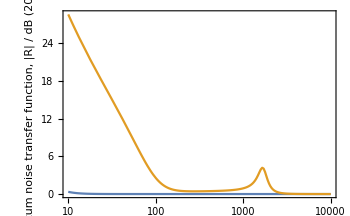
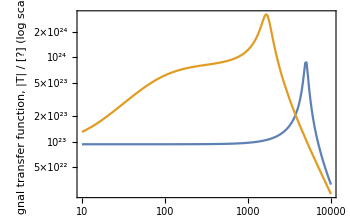
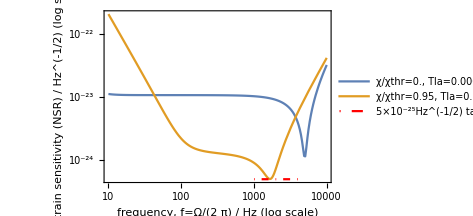

```mathematica
setConfigParamsLi2020[]
printParams[]

(*{Ω,χ,γa,γbtot,γctot,Rpd,ρRP0or1}*)
valsListList1={{0,Tla0,Tlb0,Tlc0,Rpd0,1},{0.95 HoldForm[singularityThr[Tla0,Tlb0,Tlc0]],Tla0,Tlb0,Tlc0,Rpd0,1}};
plotwReadout[valsListList1]
```

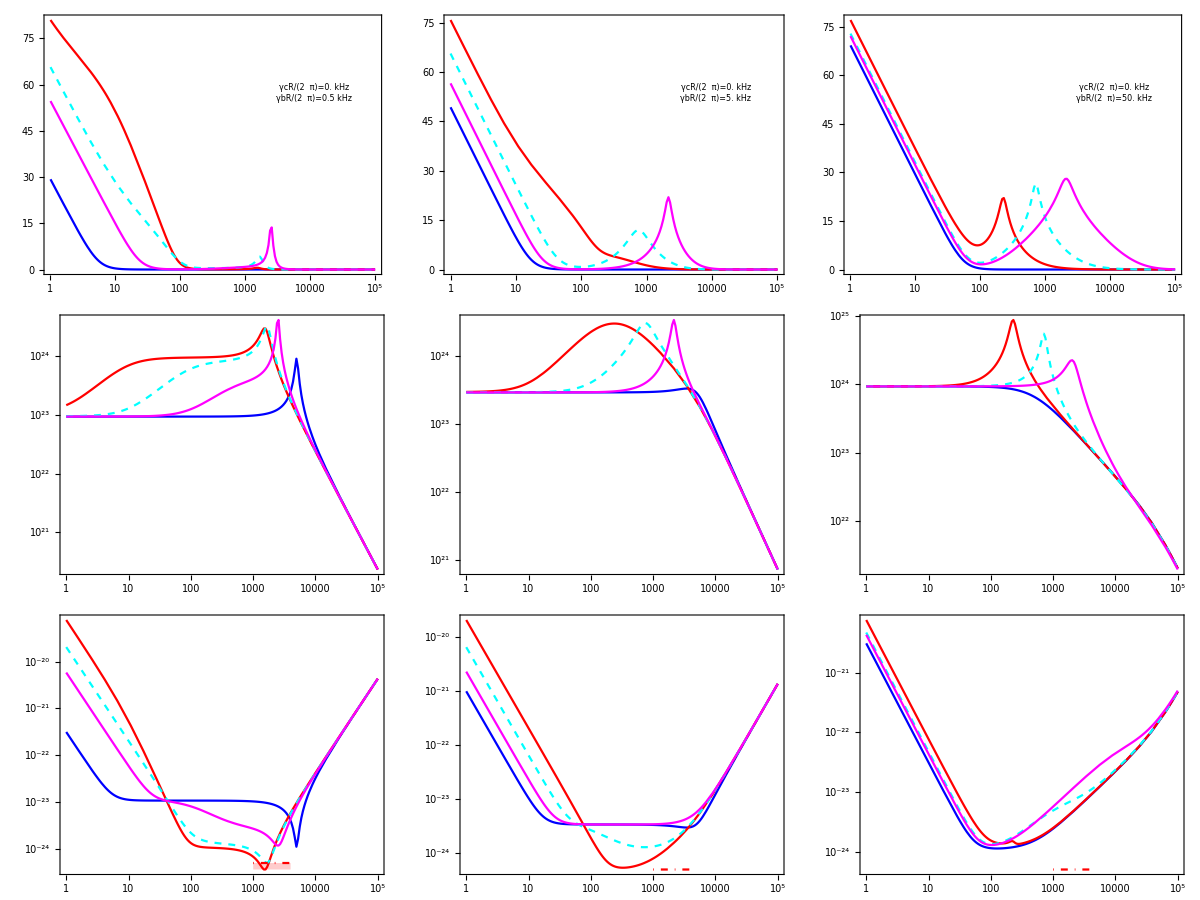
-Graphics-nondegenerate internal squeezing
parameters of Li et al, 2020 + idler sees SRM | signal | quantum noise
sensitivity (NSR) | transfer function | transfer function
/ Hz^(-1/2) (log scale) | / [?] (log scale) | / dB (20 log_10)frequency, f=Ω/(2  π) / Hz (log scale)

```mathematica
χRatio0=0.95;
Tla1=0.5Tla0;
idlerLossList={100.,1000.,10000.} 10^-6;
valsListList2={
{0,Tla1,Tlb0,idlerLossList[[1]],Rpd0,1},
{χRatio0 Hold[singularityThr[Tla1,Tlb0,idlerLossList[[1]]]],Tla1,Tlb0,idlerLossList[[1]],Rpd0,1},
{χRatio0 Hold[singularityThr[Tla1,Tlb0,idlerLossList[[2]]]],Tla1,Tlb0,idlerLossList[[2]],Rpd0,1},
{χRatio0 Hold[singularityThr[Tla1,Tlb0,idlerLossList[[3]]]],Tla1,Tlb0,idlerLossList[[3]],Rpd0,1}};
plotγbcRGrid[{2./10^6,4. 10^3,None,3. 10^6,None,0.046,200.,"Li et al, 2020 + idler sees SRM",(*γcR=*)2 π 500.,(*γbR=*)2 π 500.,2 π 5000.},{{(*γcR=*)2 π 0.,(*γbR=*)2 π 500.},{(*γcR=*)2 π 0.,(*γbR=*)2 π 5000.},{(*γcR=*)2 π 0.,(*γbR=*)2 π 50000.}},valsListList2,"signal",{Blue,Red,{Cyan,Dashed},Magenta},{1,10^5}]
(*recovers previous plot, just remember that magenta line is at a different idler loss, previously at whatever γR for open SRM (see Tsrm) corresponds, now just 10000ppm*)
```

configuration parameters:
paramSetName=Li et al, 2020 + idler sees SRM, λ0=2.×10^-6 m, Larm=4. km, Lsrc=Lsrc m, Pcirc=3. MW, Titm=Titm, Tsrm=0.046, M=200. kg
derived parameters:
ωFSR/(2  π)=1/τRoundTripArm=37.5 kHz, 1/τRoundTripSRC=133. kHz, γbR/(2  π)=0.5 kHz, γcR/(2  π)=0.5 kHz, ωs/(2  π)=5. kHz; ωs/γbR=10.

Power::infy: Infinite expression 1/0^2 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

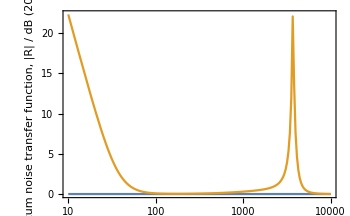
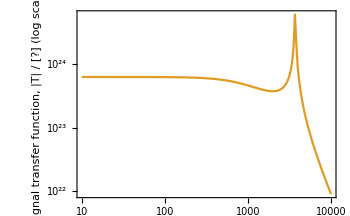
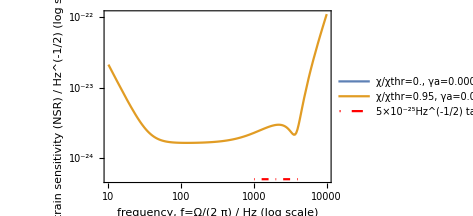

```mathematica
setConfigParamsCustom[2./10^6,4. 10^3,None,3. 10^6,None,0.046,200.,"Li et al, 2020 + idler sees SRM",(*γcR=*)2 π 500.,(*γbR=*)2 π 500.,2 π 5000.]
printParams[]

(*{Ω,χ,γa,γbtot,γctot,Rpd,ρRP0or1}*)
valsListList1={{0,Tla0,Tlb0,Tlc0,Rpd0,1},{0.95 HoldForm[singularityThr[Tla0,Tlb0,Tlc0]],Tla0,Tlb0,Tlc0,Rpd0,1}};
plotwReadout[valsListList1,"idler"]
(*1/0 errors are caused by χ=0, since then no signal can enter the idler mode*)
```

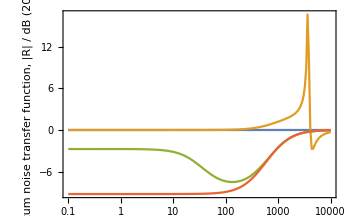
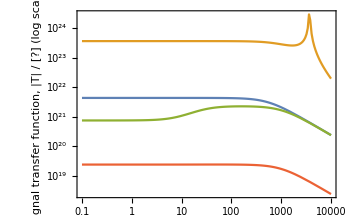
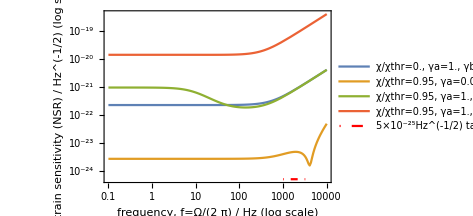

```mathematica
(*{Ω,χ,γa,γbtot,γctot,Rpd,ρRP0or1,ϕ,ψ0,ψ1,ψ2}*)
Tla1=1-10^-100;
valsListListSlow1={{0,Tla1,Tlb0,Tlc0,Rpd0,0,π/2,π/2,(*=ϕ=*)π/2,π/4},{0.95 HoldForm[singularityThr[Tla0,Tlb0,Tlc0]],Tla0,Tlb0,Tlc0,Rpd0,0,π/2,π/2,(*=ϕ=*)π/2,π/4},{0.95 HoldForm[singularityThr[Tla1,Tlb0,Tlc0]],Tla1,Tlb0,Tlc0,Rpd0,0,π/2,π/2,(*=ϕ=*)π/2,π/4},{0.95 HoldForm[singularityThr[1-10^-10000,Tlb0,Tlc0]],1-10^-10000,Tlb0,Tlc0,Rpd0,0,π/2,π/2,(*=ϕ=*)π/2,π/4}};
plotwReadout[valsListListSlow1,"combined",None,{},{0.1,10^4}]
```